## Phasenraum ohne Gaußverbreiterung

```mathematica
γ=1; B1=1; νres=1; c=0.1;
u[ν_]:= 2 π (νres-ν)/(γ B1);
MzNorm[Φ0_,ν_]=1/(1+u[ν]^2)(u[ν]^2+Cos[Φ0 √(1+u[ν]^2)]);
Plot3D[MzNorm[Φ0,ν],{Φ0,0,20},{ν,-0,2},ColorFunction->"RustTones", PlotRange->Full,Mesh->None,PlotPoints->300,Boxed->False,PlotLabel->"Phasenraum ohne Gaußverbreiterung",AxesLabel->{"Normierte Einstrahlintensität","normierte Frequenz","Signal"},LabelStyle->Large]
```

-Graphics3D-

## Phasenraum mit Gaußverbreiterung

```mathematica
γ=1; B1=1; νres=1; c=0.05;
u[ν_]:= 2 π (νres-ν)/(γ B1);
MzNorm[Φ0_,ν_]:=NIntegrate[1/(1+u[ν]^2)(u[ν]^2+Cos[Φ √(1+u[ν]^2)])*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c Φ0)],{Φ,−Infinity,Infinity}];
Plot3D[MzNorm[Φ0,ν],{Φ0,0.1,20},{ν,1,1.5},ColorFunction->"RustTones", PlotRange->Full,Mesh->None,PlotPoints->50,Boxed->False,PlotLabel->"Phasenraum mit Gaußverbreiterung",AxesLabel->{"Drehwinkel","normierte Frequenz","Signal"},LabelStyle->Directive[Bold]]
```

## Experimentelle Daten Symmetrisieren

```mathematica
Dataminmax=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-AM-1500Hz-minmax.dat", "Table"];
Dataminmax=Dataminmax[[14;;]]; k=0.85; l=1.14;
Datamaxmin=Transpose[{Dataminmax[[All,1]],(Dataminmax[[All,2]]*2/k/l+Dataminmax[[All,2]]^2/l/k^2)}];
Manipulate[ListPlot[Dataminmax, PlotRange->{-1,1}],{{k,0.85},0.001,2},{{l,1.14},1,1.5}]
ExSymData=(Data[[All,2]]*2/k/l+Data[[All,2]]^2/l/k^2)/.{k->0.85,l->1.14};
```

{{0.405395,-0.623024},{0.405334,-0.620985},{0.405273,-0.629759},{0.405212,-0.628755},{0.405151,-0.613787},{0.40509,-0.622005},{0.405029,-0.597314},{0.404968,-0.594461},{0.404908,-0.630762},«6383»,{0.015883,-0.439136},{0.015822,-0.431536},{0.015761,-0.426131},{0.0157,-0.419786},{0.015639,-0.412021},{0.015578,-0.407423},{0.015517,-0.453263},{0.015456,-0.442689},{0.015395,-0.441357}}

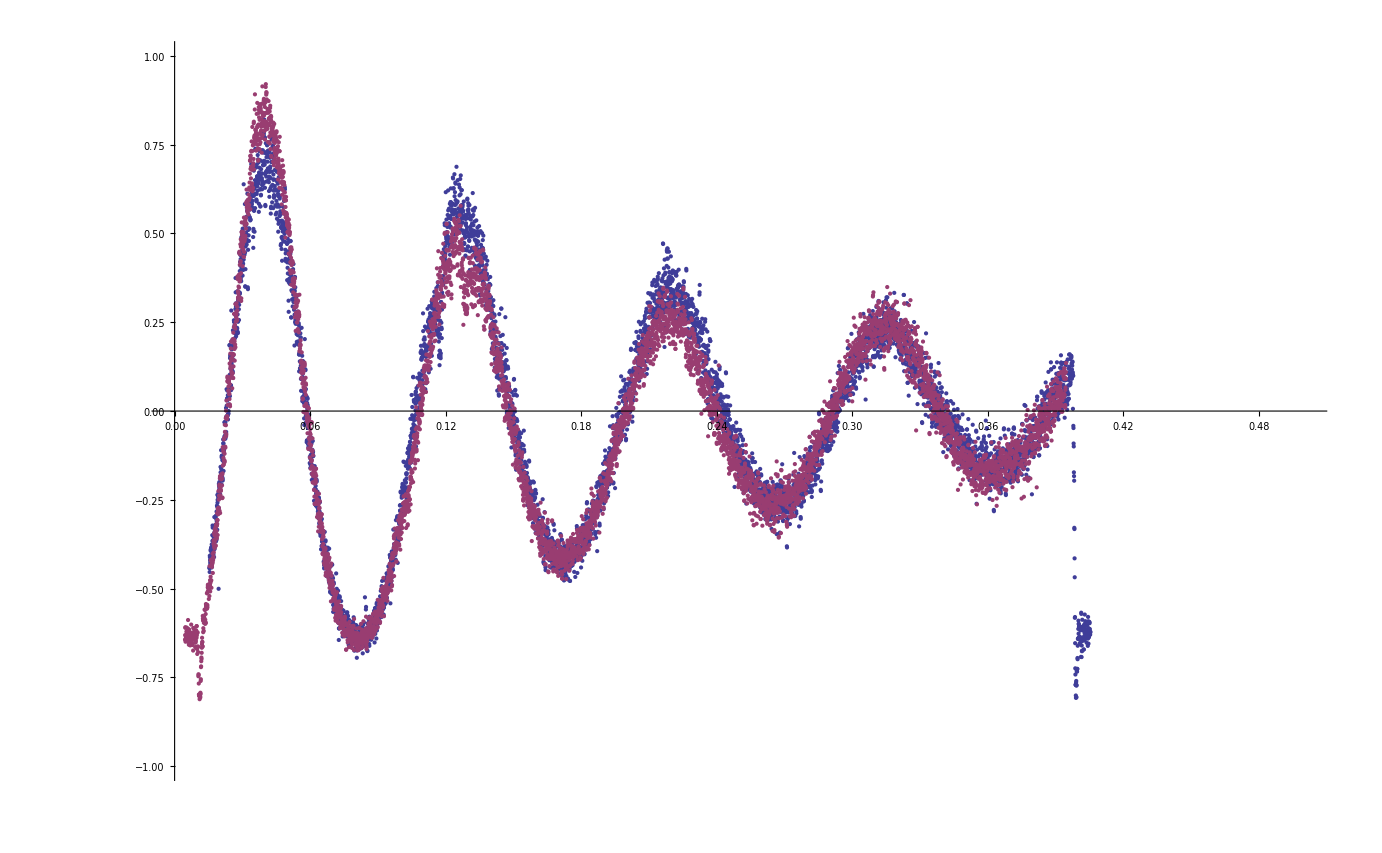

```mathematica
Dataxn=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-AM-1500Hz-maxmin.dat", "Table"];
Datanx=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-AM-1500Hz-minmax.dat", "Table"];
Dataxn=Dataxn[[14;;]]; 
Datanx=Datanx[[14;;]];
k=0.85; l=1.14;
Dataxn=Transpose[{Dataxn[[All,1]]+0.005395,(Dataxn[[All,2]]*2/k/l+Dataxn[[All,2]]^2/l/k^2)}]
Datanx=Transpose[{Datanx[[All,1]]-0.005395,(Datanx[[All,2]]*2/k/l+Datanx[[All,2]]^2/l/k^2)}];
ListPlot[{Dataxn,Datanx}, PlotRange->{{0,0.5},{-1,1}}]
ExSymData=Dataxn;
```

```mathematica
Transpose[{Dataxn[[All,1]]+2.005395,(Dataxn[[All,2]]*2/k/l+Dataxn[[All,2]]^2/l/k^2)}]
```

{{4.41079,-0.814644},{4.41073,-0.813516},{4.41067,-0.818301},{4.41061,-0.817763},{4.41055,-0.80945},{4.41048,-0.814082},{4.41042,-0.799672},{4.41036,-0.797912},{4.4103,-0.818837},{4.41024,-0.797244},«6382»,{4.02128,-0.67224},{4.02122,-0.664588},{4.02116,-0.659061},{4.0211,-0.652481},{4.02103,-0.644296},{4.02097,-0.63938},{4.02091,-0.686092},{4.02085,-0.67577},{4.02079,-0.674451}}

```mathematica
Dataminmax=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-AM-1500Hz-maxmin.dat", "Table"];
Dataminmax=Dataminmax[[14;;]]
Manipulate[ListPlot[(Dataminmax[[All,2]]*2/k/l+Dataminmax[[All,2]]^2/l/k^2), PlotRange->{-1,1}],{{k,0.85},0.001,2},{{l,1.14},1,1.5}]
ExSymData=(Data[[All,2]]*2/k/l+Data[[All,2]]^2/l/k^2)/.{k->0.85,l->1.14};
```

{{0.4,-0.392456},{0.399939,-0.390625},{0.399878,-0.398559},{0.399817,-0.397644},{0.399756,-0.384216},{0.399695,-0.39154},{0.399634,-0.369873},{0.399573,-0.367432},{0.399513,-0.399475},{0.399452,-0.366516},{0.399391,-0.393066},«6380»,{0.010548,-0.21698},{0.010488,-0.249329},{0.010427,-0.244141},{0.010366,-0.240478},{0.010305,-0.236206},{0.010244,-0.231018},{0.010183,-0.227966},{0.010122,-0.259094},{0.010061,-0.25177},{0.01,-0.250854}}

Part::partd: Part specification {-0.643286, -0.630762, -0.610323, -0.608584, -0.649424, -0.645557, -0.635083, -0.64685, -0.647172, -0.635413, -0.620985, -0.636735, « 27 », -0.623362, -0.630762, -0.630762, -0.640676, -0.643611, -0.645557, -0.601215, -0.645557, -0.643286, -0.62909, -0.62674, « 6350 »} is longer than depth of object.

Part::partd: Part specification {-0.643286, -0.630762, -0.610323, -0.608584, -0.649424, -0.645557, -0.635083, -0.64685, -0.647172, -0.635413, -0.620985, -0.636735, « 27 », -0.623362, -0.630762, -0.630762, -0.640676, -0.643611, -0.645557, -0.601215, -0.645557, -0.643286, -0.62909, -0.62674, « 6350 »} ⟦ « 1 » ⟧ is longer than depth of object.

Part::partd: Part specification {-0.643286, -0.630762, -0.610323, -0.608584, -0.649424, -0.645557, -0.635083, -0.64685, -0.647172, -0.635413, -0.620985, -0.636735, « 27 », -0.623362, -0.630762, -0.630762, -0.640676, -0.643611, -0.645557, -0.601215, -0.645557, -0.643286, -0.62909, -0.62674, « 6350 »} is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListPlot::lpn: 2.06398\ {-0.643286, -0.630762, -0.610323, -0.608584, -0.649424, -0.645557, -0.635083, -0.64685, -0.647172, -0.635413, -0.620985, « 29 », -0.630762, -0.630762, -0.640676, -0.643611, -0.645557, -0.601215, -0.645557, -0.643286, -0.62909, -0.62674, « 6350 »} ⟦ All, 2 ⟧ + « 19 »\ « 1 »^2 is not a list of numbers or pairs of numbers.

Part::partd: Part specification {-0.643286, -0.630762, -0.610323, -0.608584, -0.649424, -0.645557, -0.635083, -0.64685, -0.647172, -0.635413, -0.620985, -0.636735, « 27 », -0.623362, -0.630762, -0.630762, -0.640676, -0.643611, -0.645557, -0.601215, -0.645557, -0.643286, -0.62909, -0.62674, « 6350 »} is longer than depth of object.

Part::partd: Part specification {-0.643286, -0.630762, -0.610323, -0.608584, -0.649424, -0.645557, -0.635083, -0.64685, -0.647172, -0.635413, -0.620985, -0.636735, « 27 », -0.623362, -0.630762, -0.630762, -0.640676, -0.643611, -0.645557, -0.601215, -0.645557, -0.643286, -0.62909, -0.62674, « 6350 »} ⟦ « 1 » ⟧ is longer than depth of object.

Part::partd: Part specification {-0.643286, -0.630762, -0.610323, -0.608584, -0.649424, -0.645557, -0.635083, -0.64685, -0.647172, -0.635413, -0.620985, -0.636735, « 27 », -0.623362, -0.630762, -0.630762, -0.640676, -0.643611, -0.645557, -0.601215, -0.645557, -0.643286, -0.62909, -0.62674, « 6350 »} is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListPlot::lpn: 2.06398\ {-0.643286, -0.630762, -0.610323, -0.608584, -0.649424, -0.645557, -0.635083, -0.64685, -0.647172, -0.635413, -0.620985, « 29 », -0.630762, -0.630762, -0.640676, -0.643611, -0.645557, -0.601215, -0.645557, -0.643286, -0.62909, -0.62674, « 6350 »} ⟦ All, 2 ⟧ + « 19 »\ « 1 »^2 is not a list of numbers or pairs of numbers.

## Theorie nur auf der Resonanzfrequenz

```mathematica
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[Cos[Φ]*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c*Φ0)],{Φ,Φ0-5Sqrt[c Φ0/2],Φ0+5Sqrt[c Φ0/2]}];
Manipulate[Plot[-MzNormSpinDreh[Φ0/γct,c],{Φ0,0.001,7000}, PlotRange->{-1,1}, PlotPoints->10],{{c,0.12},0.001,0.5,0.01},{{γct,230},100,1000}]
```

```mathematica
Plot
```

## Experimentelle Daten

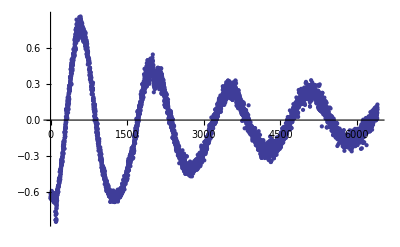

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\kl-Daten.dat", "Table"];
ExData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=Data[[n,1]],{n,1,Length[Data]}];
ListPlot[ExData]
```

## Beide Funktionen

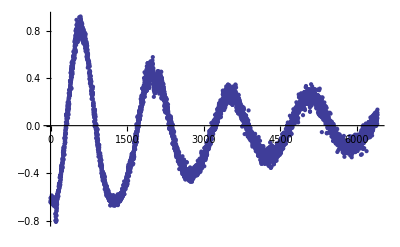

```mathematica
ListPlot[ExSymData]
```

NIntegrate::nlim: Φ = -0.114109\ √1.  + shift + 0.00416667\ (1.  + shift)
 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

Set::pspec: Part specification -179 + shift is neither an integer nor a list of integers.

Set::pspec: Part specification -178 + shift is neither an integer nor a list of integers.

Set::pspec: Part specification -177 + shift is neither an integer nor a list of integers.

General::stop: Further output of Set :: pspec will be suppressed during this calculation.

$Aborted

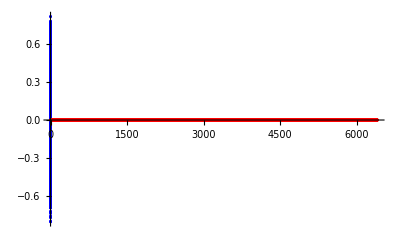

```mathematica
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[Cos[Φ]*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c*Φ0)],{Φ,Φ0-5Sqrt[c Φ0/2],Φ0+5Sqrt[c Φ0/2]}];
c=0.25; γct=240; j=1;shiftx=180;shifty=-0.01;
ExData=Table[0,{n,1,Length[Data]}];
ThData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=ExSymData[[n]],{n,1,Length[Data],j}];
Do[ThData[[Φ0-shiftx]]=1.01*(-MzNormSpinDreh[Φ0/γct,c])+shifty,{Φ0,1+shift,Length[Data]+shift,j}];
ListPlot[{ExSymData,ThData},PlotStyle->{{Blue,PointSize[0.005]},{Red,PointSize[0.005]}}, PlotRange->Full]
```

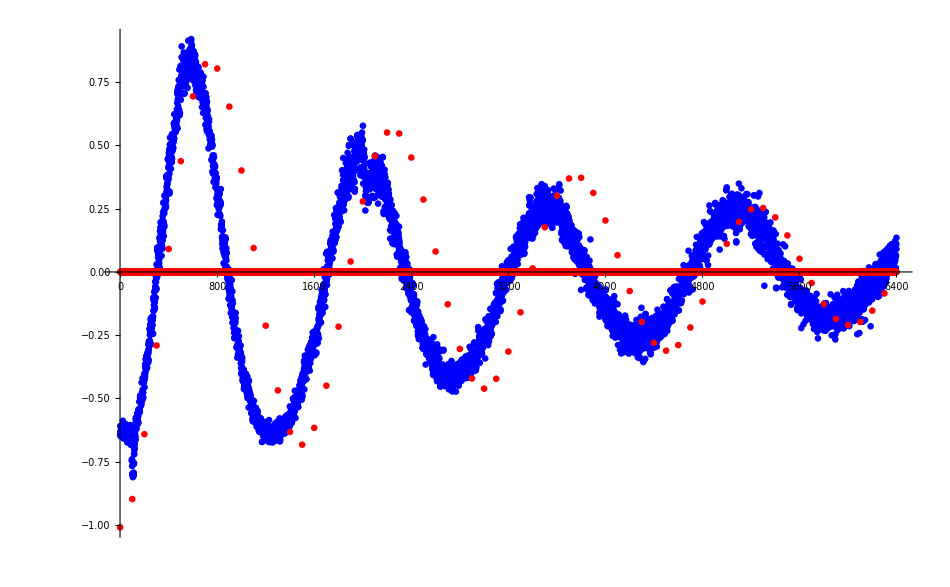

```mathematica
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[Cos[Φ]*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c*Φ0)],{Φ,Φ0-5Sqrt[c Φ0/2],Φ0+5Sqrt[c Φ0/2]}];
c=0.25; γct=240; j=100;shiftx=0;shifty=0;
ExData=Table[0,{n,1,Length[Data]}];
ThData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=ExSymData[[n]],{n,1,Length[Data],j}];
Do[ThData[[Φ0]]=1.01*(-MzNormSpinDreh[Φ0/γct,c])+shifty,{Φ0,1,Length[Data],j}];
ListPlot[{ExSymData,ThData},PlotStyle->{{Blue,PointSize[0.005]},{Red,PointSize[0.005]}}, PlotRange->Full]
```

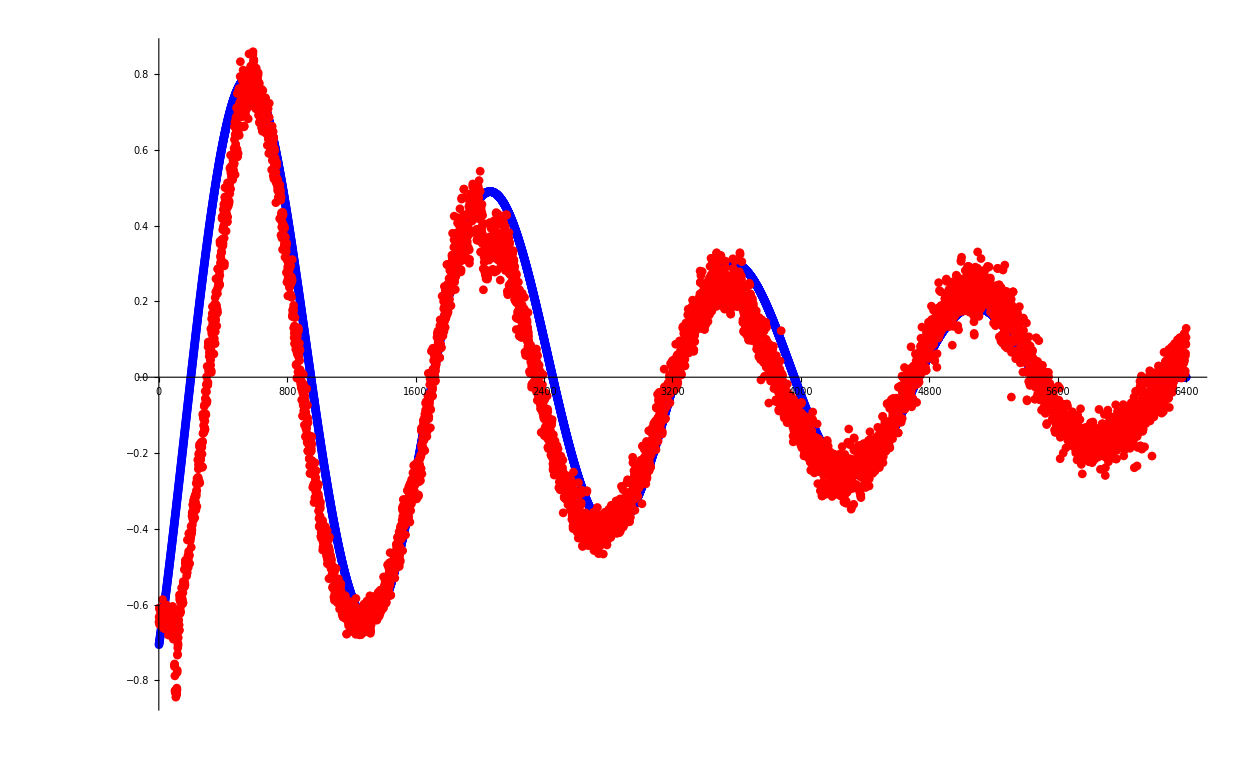

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\kl-Daten.dat", "Table"];
MzNormSpinDreh[Φ0_,c_]:=NIntegrate[Cos[Φ]*√(1/(π c Φ0))Exp[-(Φ-Φ0)^2/(c*Φ0)],{Φ,Φ0-5Sqrt[c Φ0/2],Φ0+5Sqrt[c Φ0/2]}];
c=0.30; γct=240; j=1;shiftx=180;shifty=-0.01;
ExData=Table[0,{n,1,Length[Data]}];
ThData=Table[0,{n,1,Length[Data]}];
Do[ExData[[n]]=Data[[n,1]],{n,1,Length[Data],j}];
Do[ThData[[Φ0-shiftx]]=1.01*(-MzNormSpinDreh[Φ0/γct,c])+shifty,{Φ0,1+shift,Length[Data],j}];
ListPlot[{ThData,ExData},PlotStyle->{{Blue,PointSize[0.005]},{Red,PointSize[0.005]}}, PlotRange->Full]
```

## Daten Exportieren

```mathematica
Export["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\ThData_von_Mathematica.dat",ThData]
```

D:\Git\F-Praktikum\NMR\Data-Plots\ThData_von_Mathematica.dat

## Andere Schnitte

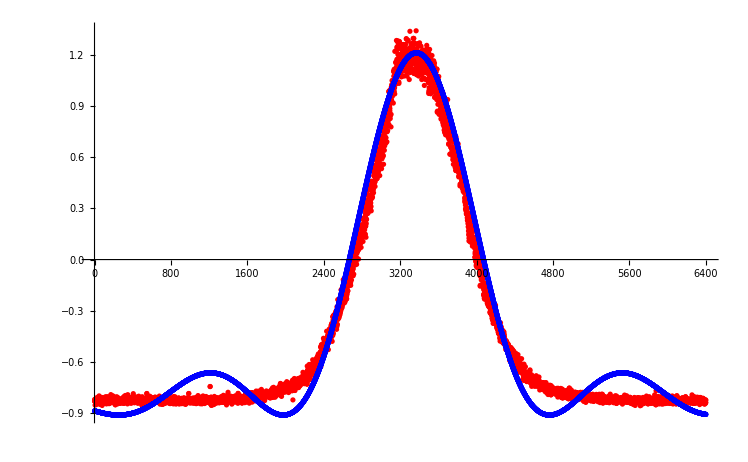

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-045mV-minmax-FM.dat", "Table"];
Data=Data[[14;;]];
k=0.85; l=1.14;
ExData=Data[[All,2]]*2/k/l+Data[[All,2]]^2/l/k^2;
γ=1; B1=1.5; νres=1; c=0.1;
u[ν_]:= 2 π (νres-ν)/(γ B1);
MzNorm[Φ0_,ν_]=1/(1+u[ν]^2)(u[ν]^2+Cos[Φ0 √(1+u[ν]^2)]);
ThData=Table[0,{n,1,Length[Data]}];
Do[ThData[[ν]]=-MzNorm[π,ν/3370]*1.06+0.15,{ν,1,Length[Data]}];
ListPlot[{ExData,ThData},PlotStyle->{{Red,PointSize[0.005]},{Blue,PointSize[0.005]}}]
```

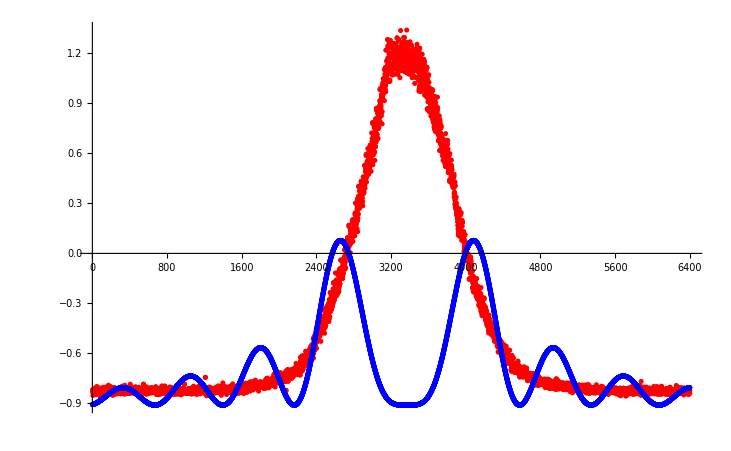

```mathematica
Data=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-045mV-minmax-FM.dat", "Table"];
Data=Data[[14;;]];
k=0.85; l=1.14;
ExData=Data[[All,2]]*2/k/l+Data[[All,2]]^2/l/k^2;
γ=1; B1=1.3; νres=1; c=0.1;
u[ν_]:= 2 π (νres-ν)/(γ B1);
MzNorm[Φ0_,ν_]=1/(1+u[ν]^2)(u[ν]^2+Cos[Φ0 √(1+u[ν]^2)]);
ThData=Table[0,{n,1,Length[Data]}];
Do[ThData[[ν]]=-MzNorm[2π,ν/3370]*1.06+0.15,{ν,1,Length[Data]}];
ListPlot[{ExData,ThData},PlotStyle->{{Red,PointSize[0.005]},{Blue,PointSize[0.005]}}]
```

```mathematica
Export["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\ExFreData_von_Mathematica.dat",ExData]
Export["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\ThFreData_von_Mathematica.dat",ThData]
```

D:\Git\F-Praktikum\NMR\Data-Plots\ExFreData_von_Mathematica.dat

D:\Git\F-Praktikum\NMR\Data-Plots\ThFreData_von_Mathematica.dat

```mathematica
Integrate[1/(1+l^2)^(3/2),{l,-Infinity, Infinity}]
```

2

```mathematica
N[Integrate[1/(1+l^2)^(3/2),{l,-4.6,4.6}]]
```

1.95435

```mathematica
Abweichung=%/2
```

0.977176